```mathematica
λ=143.099I+3.623;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→-5.28797+3.54709 ⅈ},{z→-0.0509966-7.07513 ⅈ},{z→5.34109+3.44422 ⅈ}}

-5.28797+3.54709 ⅈ

-0.0509966-7.07513 ⅈ

5.34109+3.44422 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

```mathematica
numberPoints =512;
limIterations=50;
xxMin=Re[z2]-1; xxMax=Re[z2]+1; yyMin=Im[z2]-1; yyMax=Im[z2]+1;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

```mathematica
numberPoints =512;
limIterations=50;
xxMin=-10; xxMax=10; yyMin=-10; yyMax=10;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

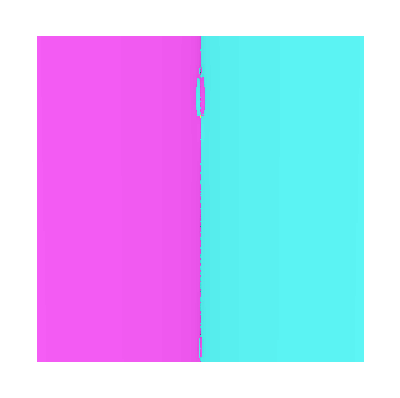

```mathematica
numberPoints =256;
limIterations=100;
xxMin=-0.25; xxMax=0.25; yyMin=0.25; yyMax=0.32;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

General::munfl: (-7.16986×10^-291+2.31632×10^-292 ⅈ) (0.000112763-0.00349044 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.-2.50521×10^-293 ⅈ)-(1.73834×10^-310-2.50521×10^-293 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.96015×10^-307+2.57163×10^-308 ⅈ) (0.000112763-0.00349044 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-5.28797+3.54709 ⅈ,-0.39422-0.226363 ⅈ,-0.761774-0.289345 ⅈ,-1.04254-0.0797524 ⅈ,-1.00187+0.00344762 ⅈ,-1.-6.38697×10^-6 ⅈ,-1.+2.73791×10^-11 ⅈ,-1.-2.95478×10^-22 ⅈ,-1.-4.70198×10^-38 ⅈ,-1.-5.22024×10^-54 ⅈ,-1.-5.79563×10^-70 ⅈ,-1.-6.43445×10^-86 ⅈ,-1.-7.14367×10^-102 ⅈ,-1.-7.93107×10^-118 ⅈ,-1.-8.80525×10^-134 ⅈ,-1.-9.7758×10^-150 ⅈ,-1.-1.08533×10^-165 ⅈ,-1.-1.20496×10^-181 ⅈ,-1.-1.33777×10^-197 ⅈ,-1.-1.48523×10^-213 ⅈ,-1.-1.64893×10^-229 ⅈ,-1.-1.83068×10^-245 ⅈ,-1.-2.03247×10^-261 ⅈ,-1.-2.25649×10^-277 ⅈ,-1.-2.50521×10^-293 ⅈ,-1.-2.78134×10^-309 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ}

```mathematica
NestList[sp,z2,10000]
```

```mathematica
NestList[sp,z3,100]
```

General::munfl: (1.-2.50521×10^-293 ⅈ)+(0.+2.50521×10^-293 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

{5.34211+3.44337 ⅈ,0.397792-0.219472 ⅈ,0.761465-0.278013 ⅈ,1.03656-0.0781058 ⅈ,1.00203+0.00295605 ⅈ,1.-5.97285×10^-6 ⅈ,1.+1.43136×10^-11 ⅈ,1.-2.12574×10^-22 ⅈ,1.-4.70198×10^-38 ⅈ,1.-5.22024×10^-54 ⅈ,1.-5.79563×10^-70 ⅈ,1.-6.43445×10^-86 ⅈ,1.-7.14367×10^-102 ⅈ,1.-7.93107×10^-118 ⅈ,1.-8.80525×10^-134 ⅈ,1.-9.7758×10^-150 ⅈ,1.-1.08533×10^-165 ⅈ,1.-1.20496×10^-181 ⅈ,1.-1.33777×10^-197 ⅈ,1.-1.48523×10^-213 ⅈ,1.-1.64893×10^-229 ⅈ,1.-1.83068×10^-245 ⅈ,1.-2.03247×10^-261 ⅈ,1.-2.25649×10^-277 ⅈ,1.-2.50521×10^-293 ⅈ,1.-2.78134×10^-309 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}